### Start choosing the example:

```mathematica
t=31;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5},Adjacency Matrix→{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{5,U1}},Switching Costs→{}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2, U1-> 0}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.010502,Null}

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→8.,u678→6.,u679→4.,u680→2.,u681→0,u682→8.,u683→-2+8.,u684→-2+6.,u685→-2+4.,u686→-2+2.,u687→0,u688→8.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→4.18612,u678→3.13959,u679→2.09306,u680→1.04653,u681→0,u682→0.+1. 4.18612,u683→0.+1. 3.13959,u684→0.+1. 2.09306,u685→0.+1. 1.04653,u686→0,u687→0,u688→0.+1. 4.18612|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.44089×10^-16

FRX1: The Error on the nonlinear terms is 4.44089×10^-16

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→4.39627,u678→3.2972,u679→2.19814,u680→1.09907,u681→0,u682→0.+1. 4.39627,u683→0.+1. 3.2972,u684→0.+1. 2.19814,u685→0.+1. 1.09907,u686→0,u687→0,u688→0.+1. 4.39627|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→4.88643,u678→3.66483,u679→2.44322,u680→1.22161,u681→0,u682→0.+1. 4.88643,u683→0.+1. 3.66483,u684→0.+1. 2.44322,u685→0.+1. 1.22161,u686→0,u687→0,u688→0.+1. 4.88643|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 8.88178×10^-16

FRX1: The Error on the nonlinear terms is 8.88178×10^-16

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→7.33396,u678→5.50047,u679→3.66698,u680→1.83349,u681→0,u682→0.+1. 7.33396,u683→0.+1. 5.50047,u684→0.+1. 3.66698,u685→0.+1. 1.83349,u686→0,u687→0,u688→0.+1. 7.33396|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.44089×10^-15

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→8.,u678→6.,u679→4.,u680→2.,u681→0,u682→0.+1. 8.,u683→0.+1. 6.,u684→0.+1. 4.,u685→0.+1. 2.,u686→0,u687→0,u688→0.+1. 8.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 8.88178×10^-16

FRX1: The Error on the nonlinear terms is 8.88178×10^-16

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→9.77058,u678→7.32794,u679→4.88529,u680→2.44265,u681→0,u682→0.+1. 9.77058,u683→0.+1. 7.32794,u684→0.+1. 4.88529,u685→0.+1. 2.44265,u686→0,u687→0,u688→0.+1. 9.77058|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 8.88178×10^-16

FRX1: The Error on the nonlinear terms is 8.88178×10^-16

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→14.5709,u678→10.9282,u679→7.28546,u680→3.64273,u681→0,u682→0.+1. 14.5709,u683→0.+1. 10.9282,u684→0.+1. 7.28546,u685→0.+1. 3.64273,u686→0,u687→0,u688→0.+1. 14.5709|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→17.3829,u678→13.0372,u679→8.69147,u680→4.34573,u681→0,u682→0.+1. 17.3829,u683→0.+1. 13.0372,u684→0.+1. 8.69147,u685→0.+1. 4.34573,u686→0,u687→0,u688→0.+1. 17.3829|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→17.3863,u678→13.0397,u679→8.69314,u680→4.34657,u681→0,u682→0.+1. 17.3863,u683→0.+1. 13.0397,u684→0.+1. 8.69314,u685→0.+1. 4.34657,u686→0,u687→0,u688→0.+1. 17.3863|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 7.10543×10^-15

FRX1: The Error on the nonlinear terms is 7.10543×10^-15

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→65.4928,u678→49.1196,u679→32.7464,u680→16.3732,u681→0,u682→0.+1. 65.4928,u683→0.+1. 49.1196,u684→0.+1. 32.7464,u685→0.+1. 16.3732,u686→0,u687→0,u688→0.+1. 65.4928|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→17.5514,u678→13.1636,u679→8.77571,u680→4.38786,u681→0,u682→0.+1. 17.5514,u683→0.+1. 13.1636,u684→0.+1. 8.77571,u685→0.+1. 4.38786,u686→0,u687→0,u688→0.+1. 17.5514|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→17.7231,u678→13.2923,u679→8.86156,u680→4.43078,u681→0,u682→0.+1. 17.7231,u683→0.+1. 13.2923,u684→0.+1. 8.86156,u685→0.+1. 4.43078,u686→0,u687→0,u688→0.+1. 17.7231|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→18.0765,u678→13.5573,u679→9.03823,u680→4.51911,u681→0,u682→0.+1. 18.0765,u683→0.+1. 13.5573,u684→0.+1. 9.03823,u685→0.+1. 4.51911,u686→0,u687→0,u688→0.+1. 18.0765|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→19.2234,u678→14.4175,u679→9.61169,u680→4.80584,u681→0,u682→0.+1. 19.2234,u683→0.+1. 14.4175,u684→0.+1. 9.61169,u685→0.+1. 4.80584,u686→0,u687→0,u688→0.+1. 19.2234|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→21.4823,u678→16.1117,u679→10.7411,u680→5.37057,u681→0,u682→0.+1. 21.4823,u683→0.+1. 16.1117,u684→0.+1. 10.7411,u685→0.+1. 5.37057,u686→0,u687→0,u688→0.+1. 21.4823|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→27.9637,u678→20.9727,u679→13.9818,u680→6.99091,u681→0,u682→0.+1. 27.9637,u683→0.+1. 20.9727,u684→0.+1. 13.9818,u685→0.+1. 6.99091,u686→0,u687→0,u688→0.+1. 27.9637|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→39.5765,u678→29.6824,u679→19.7883,u680→9.89413,u681→0,u682→0.+1. 39.5765,u683→0.+1. 29.6824,u684→0.+1. 19.7883,u685→0.+1. 9.89413,u686→0,u687→0,u688→0.+1. 39.5765|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 7.10543×10^-15

FRX1: The Error on the nonlinear terms is 7.10543×10^-15

<|j655→2,j656→2,j657→2,j658→2,j659→2,j660→2,j661→0,j662→0,j663→0,j664→0,j665→0,j666→0,jt667→0,jt668→2,jt669→2,jt670→0,jt671→2,jt672→0,jt673→2,jt674→0,jt675→2,jt676→0,u677→65.4928,u678→49.1196,u679→32.7464,u680→16.3732,u681→0,u682→0.+1. 65.4928,u683→0.+1. 49.1196,u684→0.+1. 32.7464,u685→0.+1. 16.3732,u686→0,u687→0,u688→0.+1. 65.4928|>

### What we this plot for?

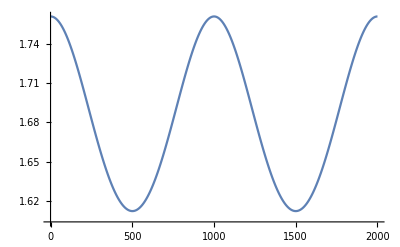

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.